```mathematica
Rutinas SSA
ScreeSSA[Serie_,L_]:=(
X=Partition[Serie,L,1];
r=MatrixRank[X];
σ=SingularValueList[N[X],r];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

PartialScreeSSA[Serie_,L_,rMax_]:=(
X=Partition[Serie,L,1];
Σ=SingularValueList[N[X],rMax][[2]];
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

CompleteSSA[Serie_,L_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],r];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,r}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
(* matrices elementales *)
For[k=1,k≤r,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤r,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=20;
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
;)

PartialSSA[Serie_,L_,rMax_,gYesNo_,wYesNo_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],rMax];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
If[gYesNo=="Yes",{
(* matrices elementales *)
For[k=1,k≤rMax,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤rMax,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
}];
If[wYesNo=="Yes",{
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=Min[20,rMax];
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
}]
;)

SetDirectory["C:\Users\sqrf\Documents\Carbono Negro"]
Semana = 1

Dat=Import["2015-CCA-PM2.5(by weeks).xlsx",{"Data",1,All, Semana+1}];
Datos =Transpose[Table[Dat, {1}]]
(*{"Data",# of sheet(s),# of row(s),# of column(s)}
*)
{M,T}=Dimensions[Datos]

Clear[U,Σ,V,r,σ,λ]
r=MatrixRank[Transpose[Datos]]
{U,Σ,V}=SingularValueDecomposition[N[Datos],r]

Clear[r,σ]
r=MatrixRank[Transpose[Datos]]
σ=SingularValueList[N[Transpose[Datos]],r]
λ=σ^2;
λLog=Table[{Log10[k],Log10[λ[[k]]]},{k,1,r}]

Serie=Flatten[Join[Table[Datos[[All,t]],{t,1,T}]]];

ListLinePlot[Serie]

L=48;
ScreeSSA[Serie,L];
```

Rutinas SSA

C:\Users\sqrf\Documents\Carbono Negro

1

{{118.},{14.},{18.},{13.},{10.},{49.},{6.},{6.},{22.},{13.},{33.},{44.},{24.},{31.},{25.},{24.},{23.},{33.},{21.},{16.},{14.},{11.},{18.},{22.},{14.},{5.},{3.},{13.},{13.},{10.},{33.},{6.},{7.},{20.},{12.},{20.},{17.},{8.},{13.},{9.},{15.},{32.},{35.},{14.},{14.},{18.},{15.},{21.},{27.},{11.},{22.},{25.},{23.},{40.},{10.},{24.},{20.},{41.},{18.},{16.},{3.},{8.},{10.},{18.},{11.},{1.},{2.},{8.},{3.},{11.},{10.},{16.},{34.},{24.},{9.},{12.},{13.},{12.},{4.},{41.},{22.},{6.},{13.},{19.},{19.},{15.},{11.},{0.},{0.},{26.},{37.},{37.},{22.},{7.},{23.},{33.},{25.},{27.},{19.},{24.},{22.},{27.},{16.},{29.},{10.},{15.},{26.},{0.},{23.},{23.},{29.},{21.},{25.},{24.},{21.},{27.},{13.},{25.},{14.},{21.},{5.},{17.},{17.},{17.},{13.},{15.},{14.},{13.},{21.},{11.},{16.},{9.},{27.},{9.},{14.},{21.},{15.},{22.},{26.},{20.},{10.},{24.},{27.},{11.},{16.},{14.},{1.},{13.},{45.},{39.},{11.},{11.},{2.},{10.},{29.},{12.},{4.},{8.},{11.},{16.},{24.},{31.},{35.},{25.},{37.},{26.},{29.},{10.},{12.},{15.},{21.},{7.},{14.},{24.},{25.},{24.},{12.},{16.},{21.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{20.},{17.},{13.},{19.},{11.},{21.},{34.},{35.},{24.},{19.},{24.},{14.},{6.},{12.},{18.},{10.},{10.},{8.},{18.},{8.},{14.},{19.},{23.},{25.},{0.},{0.},{12.},{10.},{12.},{12.},{17.},{16.},{0.},{18.},{30.},{25.},{15.},{8.},{14.},{21.},{16.},{13.},{7.},{25.},{31.},{24.},{18.},{6.},{19.},{11.},{11.},{24.},{16.},{26.},{37.},{23.},{11.},{7.},{10.},{17.},{21.},{13.},{7.},{22.},{24.},{0.},{22.},{22.},{18.},{16.},{24.},{6.},{13.},{7.},{10.},{7.},{1.},{4.},{14.},{21.},{8.},{6.},{8.},{6.},{0.},{0.},{7.},{11.},{6.},{14.},{1.},{6.},{16.},{18.},{13.},{7.},{5.},{16.},{4.},{12.},{6.},{7.},{5.},{10.},{20.},{23.},{26.},{17.},{8.},{20.},{29.},{25.},{26.},{72.},{67.},{20.},{31.},{16.},{25.},{10.},{0.},{30.},{8.},{28.},{36.},{42.},{44.},{8.},{6.},{0.},{5.},{22.},{21.},{18.},{32.},{24.},{24.},{24.},{47.},{19.},{9.},{11.},{18.},{25.}}

{336,1}

1

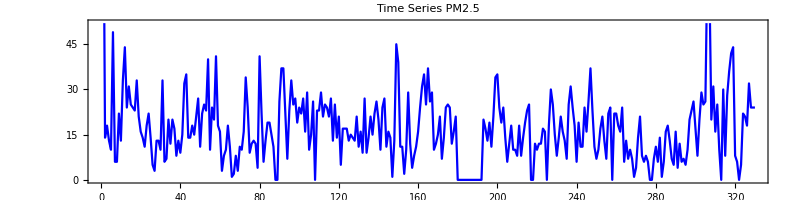

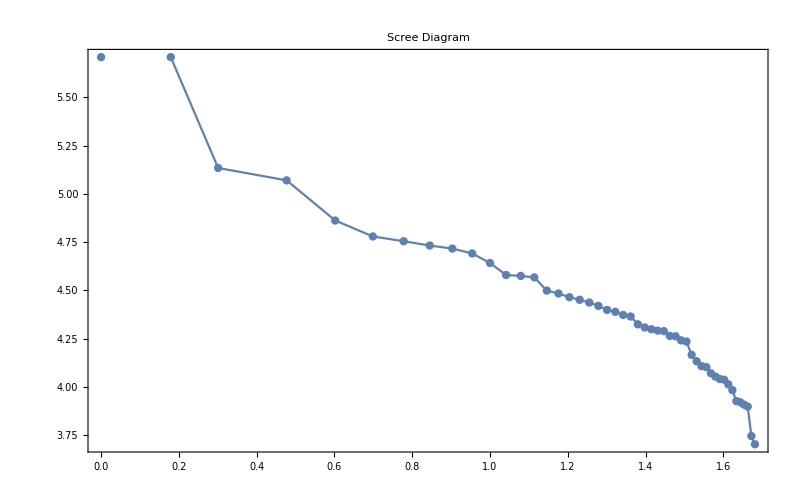

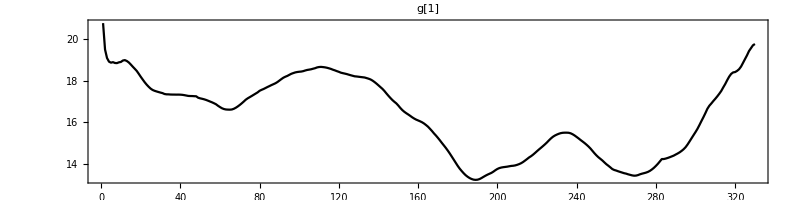

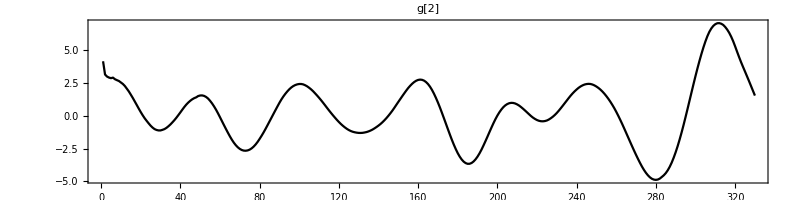

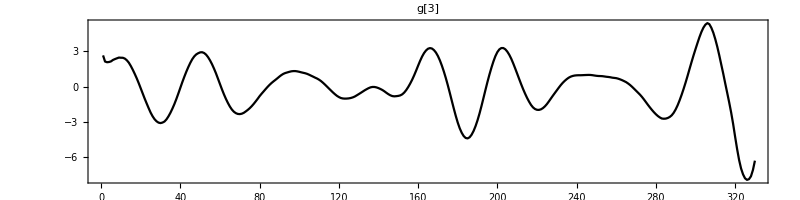

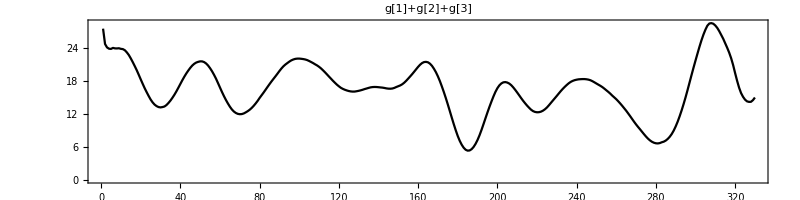

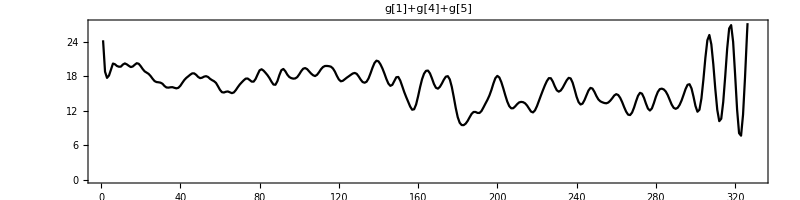

5

{31.0358,24.0625,22.7687,23.1233,24.1544,25.3685,25.1941,24.8917,24.7597,24.651,24.8925,24.8631,24.3506,23.688,22.9477,22.474,22.1539,21.7713,20.9898,19.8802,18.6958,17.6244,16.8008,15.9898,15.0576,14.1296,13.3601,12.9452,12.7556,12.6536,12.5534,12.3106,12.3324,12.6825,13.1832,13.7174,14.1643,14.6852,15.4457,16.4774,17.6831,18.8273,19.8034,20.6297,21.4097,22.0598,22.3869,22.3665,22.2017,22.1129,22.2117,22.2946,22.1484,21.6736,20.9088,20.1611,19.3739,18.4231,17.1128,15.7437,14.583,13.8054,13.2526,12.6691,11.9416,11.2839,10.9891,11.0788,11.3629,11.6904,12.0115,12.3922,12.7884,12.9584,12.9105,12.896,13.2227,14.0638,15.2491,16.4248,17.0574,17.2667,17.3544,17.4112,17.3666,17.2005,17.128,17.5071,18.5564,20.0276,21.2621,21.8042,21.6895,21.3262,21.1325,21.1204,21.1568,21.2743,21.529,21.9948,22.507,22.8656,22.8718,22.5496,21.9782,21.3967,20.8863,20.4984,20.473,20.6499,20.8703,20.9161,20.7433,20.3902,19.9855,19.5452,18.8976,18.0219,16.9703,16.0759,15.5186,15.4279,15.5574,15.724,15.8863,16.0912,16.3171,16.45,16.3714,16.0047,15.5621,15.2498,15.2625,15.5712,16.2845,17.305,18.3877,19.2938,19.7567,19.69,19.2203,18.5515,17.7152,16.8012,16.0698,15.7675,16.0813,16.9333,17.8261,18.1299,17.7613,17.0978,16.4556,15.9968,15.6349,15.2768,15.2085,15.7901,17.1261,19.0223,21.0345,22.7625,23.9658,24.5699,24.6035,23.9694,22.8263,21.4399,20.2506,19.4483,19.0131,18.7414,18.5002,18.0458,17.1075,15.488,13.1399,10.3308,7.46335,4.98394,3.25984,2.26127,1.80431,1.78091,2.16461,2.88934,3.75968,4.5278,5.10139,5.64271,6.46067,7.72201,9.3424,11.0271,12.6827,14.4113,16.2856,18.2607,19.9627,20.987,21.1928,20.7194,19.8179,18.6624,17.4703,16.4738,15.7813,15.3945,15.2385,15.1166,14.8762,14.408,13.8116,13.0922,12.2077,11.2152,10.2793,9.80332,9.92621,10.5104,11.3687,12.3127,13.3074,14.3285,15.3052,16.112,16.4326,16.2116,15.7438,15.4464,15.6084,16.2111,17.0907,18.098,19.0678,19.8118,19.9887,19.4808,18.4873,17.3831,16.5993,16.2868,16.5321,17.2287,18.1101,18.9415,19.3799,19.2074,18.5468,17.7,16.9885,16.5309,16.2088,15.8974,15.6335,15.55,15.6222,15.7725,15.9708,15.8987,15.4088,14.5464,13.4185,12.1293,10.9227,9.94234,9.40132,9.3442,9.71337,10.301,10.7803,10.8225,10.2006,9.0171,7.56193,6.27762,5.56484,5.60881,6.27972,7.16785,7.89996,8.33343,8.44633,8.41806,8.23773,7.88065,7.41042,7.04696,7.07773,7.61641,8.60836,10.0485,11.8255,13.8784,16.0181,17.9367,19.2621,19.7425,19.5026,19.0341,19.1493,20.557,23.5001,27.6446,32.1322,35.7039,36.8619,35.193,31.5015,26.813,22.6083,19.9368,19.5349,21.5686,25.009,28.8592,31.2923,30.71,26.4888,19.3365,11.818,6.38332,4.83106,7.5926,13.3557,20.3836,26.9642,31.0809,32.3639,30.688}

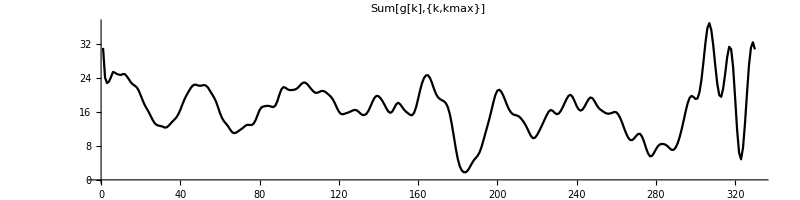

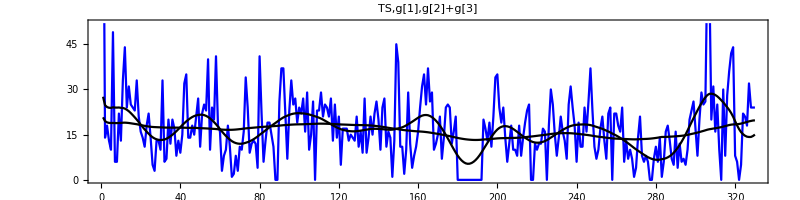

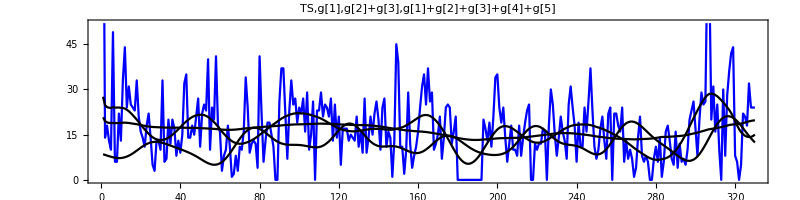

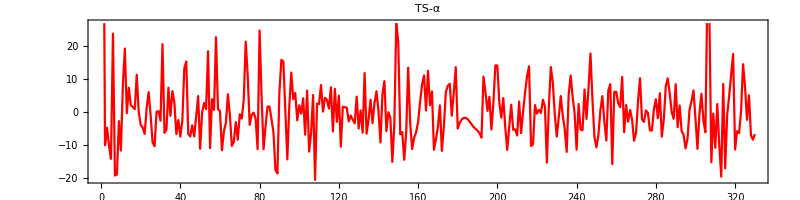

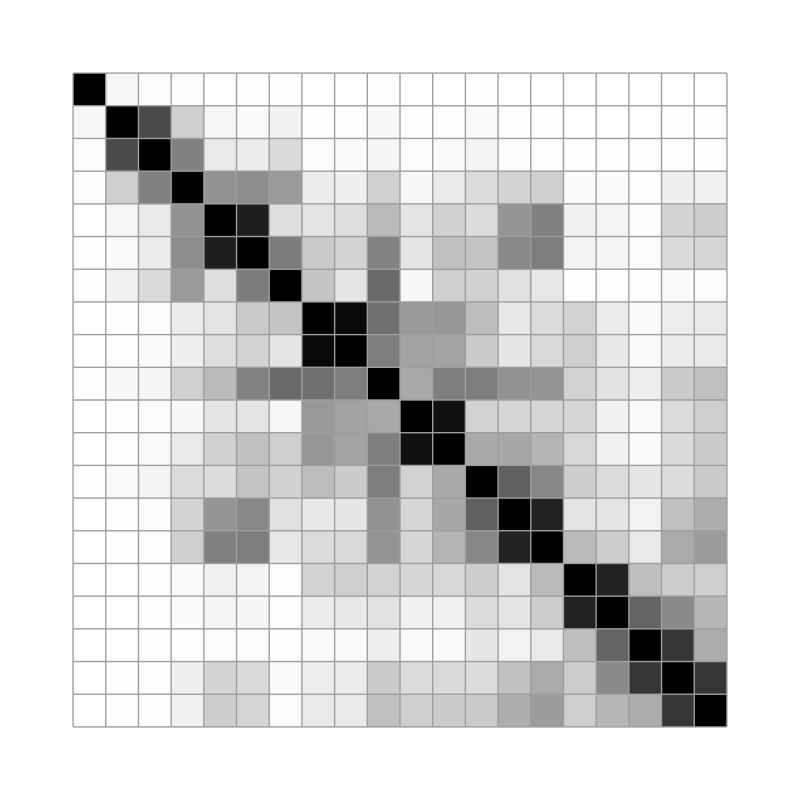

86.96417802489759
-10.062453875135642
-4.768707520009961
-10.123343636380408
-14.154408284408738
23.631472717798886
-19.194066909468134
-18.89168667503956
-2.759684260306045
-11.651023967555616
8.107517736288116
19.136873476482627
-0.350640470163988
7.312037613881824
2.0522534205188165
1.5259876442859905
0.8460955532109615
11.228705761381327
0.010196104714246701
-3.8801614643864895
-4.695792043099637
-6.624366041913085
1.1992224540770344
6.010202493118058
-1.057642363033633
-9.129558918244163
-10.360101653002756
0.054795039768041676
0.24440790035746573
-2.653646389536231
20.446575875513616
-6.310592045843688
-5.332365750821625
7.317541157263824
-1.1832070812931903
6.282582823556975
2.8357454709102132
-6.685232910255298
-2.4457487779821356
-7.477365877355648
-2.6830707760906236
13.172703501111595
15.196559036567137
-6.629717328723174
-7.409672375069118
-4.059813114638239
-7.386918240181796
-1.3664937761849352
4.798287506423414
-11.112855105253317
-0.21169625000228365
2.7054161542692157
0.8515724516819034
18.326409316403293
-10.908757050991863
3.8388885400492754
0.6260847599184203
22.576850399562474
0.8872211829310679
0.25632456870826736
-11.582961028607086
-5.805374146699656
-3.2526092116389407
5.330894918547379
-0.9416121297115545
-10.283893347514628
-8.989056708399447
-3.0788028772891973
-8.362906487885464
-0.6904315983139888
-2.0115457008270496
3.607812220497161
21.21162454636889
11.04162462023894
-3.910538238701749
-0.8960242197567574
-0.22267265964702787
-2.0638005164855002
-11.249103814893148
24.575211875306547
4.942561759781832
-11.266685407281429
-4.354415376056917
1.5888262402395306
1.6334241390387163
-2.2005157660907066
-6.127987267782888
-17.50713730349661
-18.55644377569467
5.972394882940584
15.73790797365389
15.195825886769164
0.3104993653802133
-14.326155941140843
1.8674826844323604
11.87958007107721
3.843222775648478
5.725710004160447
-2.529000610091689
2.005169178519779
-0.5070081421275958
4.1343828114008545
-6.871805576853433
6.450375184148896
-11.978160065827542
-6.396745247088393
5.113735497730051
-20.498437682758528
2.5269785958801805
2.350101114959365
8.129705122726516
0.0839156373235781
4.256691485308654
3.6097963085176374
1.014470854718418
7.4547797496646915
-5.89760207524332
6.978088951637044
-2.9702564071089768
4.924149093592199
-10.518601851976717
1.5720631702352357
1.4425887875441497
1.2760233207945788
-2.8862719868206312
-1.0911811687279496
-2.3170809991749053
-3.449962203739748
4.6286190126384525
-5.004691320102765
0.4379062833695535
-6.24983986484496
11.73748943079919
-6.57116412839814
-2.28449685822423
3.6949943213214844
-3.3876769367825688
2.7061606225525487
6.2432820782376055
0.30996173750019196
-9.22033864334907
5.4484764679112985
9.284752693497225
-5.801163061702997
-0.06984887368242809
-1.767477972787761
-15.081302721884466
-3.9333325878622816
27.173934213526405
20.8701080565668
-6.761340714928878
-6.097767439039213
-14.455617120383017
-5.996843355056168
13.365144076667509
-3.276808399111964
-11.208501010734054
-7.790063358444046
-6.126130568366097
-3.0223388670217197
2.965500429368454
8.237518049391927
11.034219036466801
0.4300532222259932
12.3965418315126
2.0305702572384625
6.1736740004498145
-11.439902033778544
-8.250553563771359
-4.4482796427917215
1.986869410751062
-11.741419612982067
-4.500210478414161
5.954199653891163
7.892506178442357
8.511986473443228
-1.139878645279083
5.669166845613994
13.53664791537637
-4.983941703116436
-3.2598362160223306
-2.261271003701694
-1.8043060378881073
-1.780913201628481
-2.164614058408583
-2.8893381163053284
-3.7596840614209057
-4.527802154777524
-5.1013906615607105
-5.642714909700236
-6.460674098496481
-7.7220098733265985
10.657603387439883
5.972911341922655
0.3173232654356539
4.588730950298848
-5.285590979194833
2.7392886931960234
14.037275631460048
14.013011836170463
2.807160138720299
-1.7194199048164762
4.182062910376793
-4.662368050480822
-11.470297279953023
-4.47381805670469
2.218709799758658
-5.394491221964316
-5.2384536638464105
-7.1165535327680765
3.123823286403054
-6.408004062615452
0.18835394859426913
5.907849782270416
10.792321557772045
13.784820703061035
-10.27928644858467
-9.803321596157343
2.0737851385665707
-0.5104163200513803
0.6312965121266334
-0.312747872032098
3.6925639617842503
1.6715417269175603
-15.305181382365948
1.8880232233918228
13.567364233361545
8.788410429721988
-0.7437761888082708
-7.446362402907303
-1.6084394198351877
4.7889267826436495
-1.0907332541722106
-5.098028766974593
-12.067751731992963
5.188208932411452
11.011267463236784
4.519198778998685
-0.4873072151517128
-11.383083035529587
2.400691525060868
-5.286820362461757
-5.532142551150816
6.771319920783203
-2.1100724046499657
7.058495594255891
17.620086852439755
3.7925928159999245
-7.546822034966162
-10.699967681643521
-6.9884684720038095
0.46914420373289545
4.791204417755139
-2.8973609729310645
-8.633456347961438
6.450028544261247
8.377813658832217
-15.772525383479895
6.029249309326907
6.101275205129658
2.5912043422302027
1.4536419462439412
10.58146492275892
-6.129307795362152
2.077254416103843
-2.942337954654054
0.5986750579213158
-2.3442026415292005
-8.713372936944722
-6.30095711918605
3.21966471075989
10.17746483118084
-2.2006183169949995
-3.017104787894347
0.43807010199139373
-0.27761760871124785
-5.564841919026708
-5.608813561505697
0.7202846409129693
3.8321531088013625
-1.8999616695630808
5.666571736665009
-7.44633310383316
-2.4180637507543388
7.762267454013283
10.119345914686567
5.589575218985807
-0.046956861350440526
-2.0777314238823035
8.383588496502863
-4.608361494777567
1.9515212716670511
-5.825504313320399
-6.878361518750841
-11.018142065912972
-7.936699598667548
0.7378718966510718
3.2575123368044565
6.49740090920827
-2.03411279197179
-11.149327402754885
-0.5570169986831921
5.499873839407297
-2.6446078154725186
-6.132165505842522
36.29610829949114
30.138061288943675
-15.193047387174737
-0.5014766727703659
-10.812964460201691
2.391655732334332
-9.936834894444829
-19.534915984810617
8.43138977058949
-17.009008571330696
-0.8592438865777936
4.707652274431496
11.289983937896402
17.511207396142403
-11.336543948456562
-5.818023253671992
-6.383321499131291
0.16894187617800327
14.407396551839238
7.644281229720706
-2.383606719917026
5.035843216410605
-7.080850595254951
-8.363855915065571
-6.688048067120857

```mathematica
FigSerie=ListLinePlot[Serie[[1;;330]],Frame -> True,PlotLabel->"Time Series PM2.5",LabelStyle->Directive[Bold,Orange],PlotStyle->Blue,ImageSize->800,AspectRatio->1/4]

ListLinePlot[λLog,Mesh->All,Frame -> True,PlotLabel->"Scree Diagram",LabelStyle->Directive[Bold,Orange]]

CompleteSSA[Serie[[1;;330]],L];

Fig1=ListLinePlot[g[1],Frame -> True,PlotLabel->"g[1]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig2=ListLinePlot[g[2],Frame -> True,PlotLabel->"g[2]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig3=ListLinePlot[g[3],Frame -> True,PlotLabel->"g[3]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig23=ListLinePlot[g[1]+g[2]+g[3],Frame -> True,PlotLabel->"g[1]+g[2]+g[3]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig45=ListLinePlot[g[1]+g[4]+g[5],Frame -> True,PlotLabel->"g[1]+g[4]+g[5]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

kmax =5
alpha=Sum[g[k],{k,kmax}]

Figalpha=ListLinePlot[alpha,PlotLabel->"Sum[g[k],{k,kmax}]",LabelStyle->Directive[Bold,Orange],LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Show[FigSerie,Fig1,Fig23,Frame -> True,PlotLabel->"TS,g[1],g[2]+g[3]",LabelStyle->Directive[Bold,Orange]]
Show[FigSerie,Fig1,Fig23,Fig12345,Frame -> True,PlotLabel->"TS,g[1],g[2]+g[3],g[1]+g[2]+g[3]+g[4]+g[5]",LabelStyle->Directive[Bold,Orange]]
Filtered = ListLinePlot[Serie[[1;;330]]-alpha,Frame -> True,PlotLabel->"TS-α",LabelStyle->Directive[Bold,Orange],PlotStyle->Red,ImageSize->800,AspectRatio->1/4]

ArrayPlot[wMatriz,Mesh->All,Frame->All,FrameTicks->Automatic]

ExportString[Table[ Serie[[1;;330]]-alpha],"List"]
```